```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

Below, using sparse technique methods, I will be presenting the 8 qubit models. One thinks of the qubits living on a ring such that the qubits are connected to one another. The system, cut out on plane looks like this,

```mathematica
Clear[a1,a2,a3,a4,a5,a6,at]
Visual = {{a1,at,a2,at},{a3,a4,a5,a6}};
a1=RandomReal[{0.0001,0.4999}];
a2=RandomReal[{0.0001,0.4999}];
a3=RandomReal[{0.0001,0.4999}];
a4=RandomReal[{0.0001,0.4999}];
a5=RandomReal[{0.0001,0.4999}];
a6=RandomReal[{0.0001,0.4999}];
at=RandomReal[{0.0001,0.4999}];
Image[Visual]
Clear[a1,a2,a3,a4,a5,a6,at]
```

-Graphics-

We will now write the initial density matrix,

```mathematica
RHO = KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-at,0},{0,at}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}},{{1-a5,0},{0,a5}},{{1-at,0},{0,at}},{{1-a6,0},{0,a6}}];
```

At any time in the iteration, we will pick up up sets of four given by either,

```mathematica
Clear[a1,a2]
Visual = {{a1,a1,a2,a2},{a1,a1,a2,a2}};
a1=RandomReal[{0.0001,0.4999}];
a2=RandomReal[{0.0001,0.4999}];
Image[Visual]
Clear[a1,a2]
```

-Graphics-

or we can pick them at the edges and the centre (since this is really a ring) given by,

```mathematica
Clear[a1,a2]
Visual = {{a1,a2,a2,a1},{a1,a2,a2,a1}};
a1=RandomReal[{0.0001,0.4999}];
a2=RandomReal[{0.0001,0.4999}];
Image[Visual]
Clear[a1,a2]
```

-Graphics-

Let us write the two cases separately. For case 1, the interaction is actually very straightforward given by,

```mathematica
Interaction = SparseArray[{{4,13}->I,{13,4}->-I},{16,16}];
Hcase1term1 = KroneckerProduct[Interaction, IdentityMatrix[16]];
Hcase1term2 = KroneckerProduct[IdentityMatrix[16],Interaction];
Hcase1 = Hcase1term1+Hcase1term2
Image[Hcase1term1];
Image[Hcase1term2];
```

SparseArray[…]

Image::imgarray: The specified argument … should be an array of rank 2 or 3 with machine-sized numbers.

The corresponding unitary looks like,

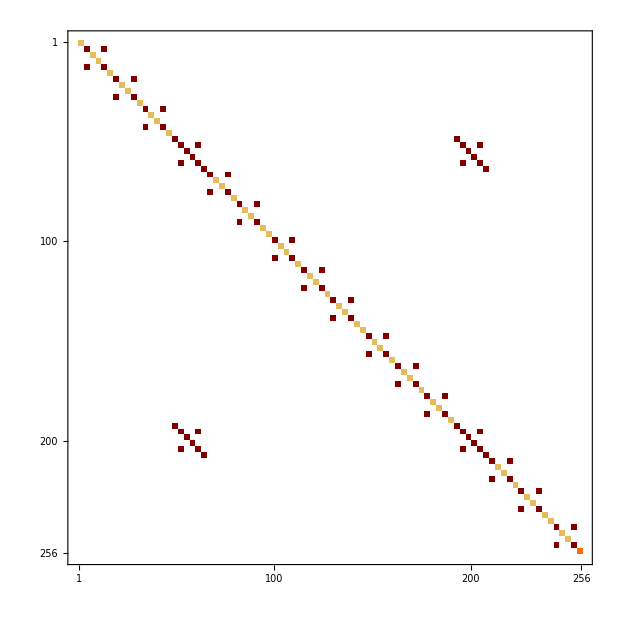

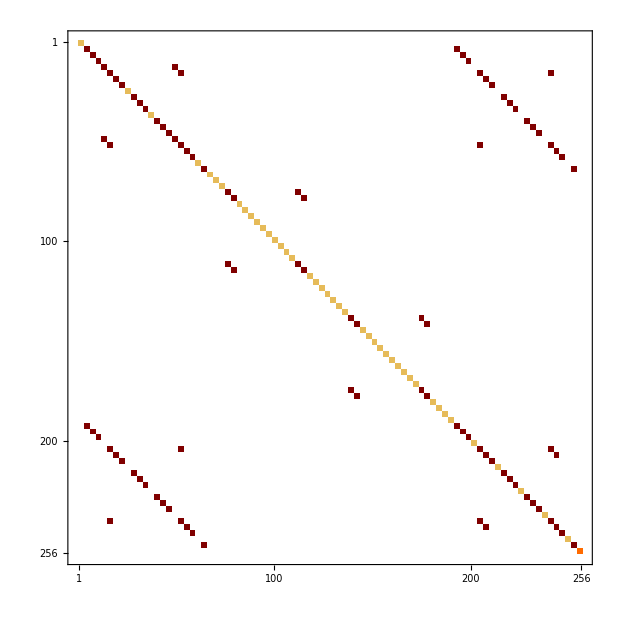

SparseArray[…]

```mathematica
InteractionUnitary = MatrixExp[- I Interaction θ];
TotalInteractionUnitaryForCase1 = MatrixExp[- I Hcase1  θ];//FullSimplify
Ucase1term1 = KroneckerProduct[InteractionUnitary, IdentityMatrix[16]];
Ucase1term2 = KroneckerProduct[IdentityMatrix[16],InteractionUnitary];
Clear[θ]
θ=RandomReal[{0,2π}];
Image[Ucase1term1];
Image[Ucase1term2];
Clear[θ]
MatrixPlot[SparseArray[TotalInteractionUnitaryForCase1]];
MatrixPlot[SparseArray[TotalInteractionUnitaryForCase2]];
```

```mathematica
RHOTcase1[θ_,a1_,a2_,at_,a3_,a4_,a5_,a6_]:=RHOTcase1[θ,a1,a2,at,a3,a4,a5,a6]=SparseArray[TotalInteractionUnitary].SparseArray[RHO].Transpose[SparseArray[TotalInteractionUnitary]]
```

```mathematica
SparseArray[TotalInteractionUnitary].SparseArray[RHO].Transpose[SparseArray[TotalInteractionUnitary]]
```

```mathematica
{197,197}/.ArrayRules[SparseArray[TotalInteractionUnitary]]
```

For case 1, the interaction is actually very straightforward given by,

```mathematica
Interaction = SparseArray[{{4,13}->I,{13,4}->-I},{16,16}];
```

```mathematica
Hcase2term1 = KroneckerProduct[IdentityMatrix[4],Interaction,IdentityMatrix[4]];
Hcase2term2 = SparseArray[{{4,193}->I,{193,4}->-I,{36,225}-> I,{225,36}->-I,{20,209}->I,{209,20}->-I,{12,201}->I,{201,12}->-I,{8,197}->I,{197,8}->-I,{52,241}->I,{241,52}->-I,{44,233}->I,{233,44}->-I,{24,213}->I,{213,24}-> -I,{40,229}->I,{229,40}->-I,{28,217}->I,{217,28}->-I,{16,205}->I,{205,16}->-I,{32,221}->I,{221,32}->-I,{48,237}->I,{237,48}->-I,{56,245}->I,{245,56}->-I,{60,249}->I,{249,60}->-I,{64,253}->I,{253,64}->-I},{256,256}];
Hcase2 = Hcase2term1+Hcase2term2;
TotalInteractionUnitaryForCase2 = MatrixExp[- I Hcase2  θ];
SparseArray[TotalInteractionUnitaryForCase2]
RHOTcase2[θ_,a1_,a2_,at_,a3_,a4_,a5_,a6_]:=RHOTcase2[θ,a1,a2,at,a3,a4,a5,a6]=SparseArray[TotalInteractionUnitaryForCase2].SparseArray[RHO].Transpose[SparseArray[TotalInteractionUnitaryForCase2]]
```

SparseArray[…]

```mathematica
Clear[RHO,RHOT]
```

```mathematica
a1=RandomReal[{0.0001,0.4999}];
a2=RandomReal[{0.0001,0.4999}];
a3=RandomReal[{0.0001,0.4999}];
a4=RandomReal[{0.0001,0.4999}];
a5=RandomReal[{0.0001,0.4999}];
a6=RandomReal[{0.0001,0.4999}];
at=RandomReal[{0.0001,0.4999}];
θ=RandomReal[{0,2π}];
```

```mathematica
RHOT=SparseArray[TotalInteractionUnitaryForCase2].SparseArray[RHO].Transpose[SparseArray[TotalInteractionUnitaryForCase2]]
```

SparseArray[…]

```mathematica
RHOTmatrix= MatrixForm[RHOT];
```

(1)
 |  |  |  |

```mathematica
TraceSystem[RHOT,{2,3,4,5,6,7,8}]
MatrixPlot[RHO];
MatrixPlot[RHOT];
;If[WorkMatrix[[1,1]]>0&&WorkMatrix[[1,2]]>0,
Print[start];Print[MatrixPlot[WorkMatrix]],Null]
```

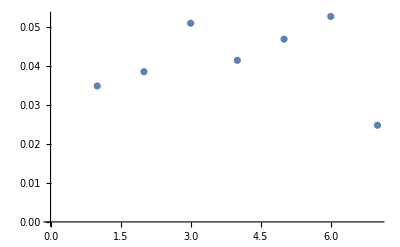

0.0546435

```mathematica
Clear[a1,a2,a3,a4,a5,a6,at,θ,i,RHOT,Qubit1,Qubit2,Qubit4,Qubit5,QubitT1,QubitT2,QubitGrad1,QubitGrad2,WEX1,WEX2]
Temp[h_]:= 1/(Log[(1-h)/h])
at=RandomReal[{0.0001,0.4999}];
a1=RandomVariate[NormalDistribution[at,0.01]];
a2=RandomVariate[NormalDistribution[at,0.01]];
a3= at-(a1-at+a2-at);
a4=RandomVariate[NormalDistribution[at,0.01]];
a5=RandomVariate[NormalDistribution[at,0.01]];
a6=at-(a4-at+a5-at);
ListPlot[{a1,a2,a3,at,a4,a5,a6}]
RandomVariate[NormalDistribution[at,0.01]]
```

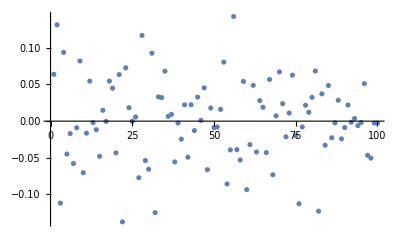

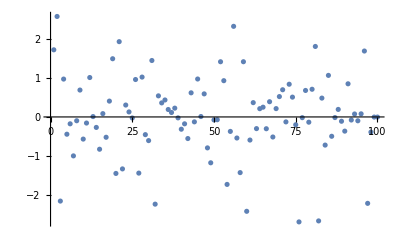

```mathematica
For[RHOT=RHO;start=1;count1=1;count2=1,count1<100;count2<100;start<100,count1++;count2++;start++,Qubitsubsys1=TraceSystem[RHOT,{3,4,5,6,7,8}];QubitT1=TraceSystem[RHOT,{1,2,4,5,6,7,8}];Qubitsubsys2=TraceSystem[RHOT,{1,2,3,4,7,8}];QubitT2=TraceSystem[RHOT,{1,2,3,4,5,6,8}];
T1=QubitT1[[2,2]];
T2=QubitT2[[2,2]];
ExtWorkInSubSys1= Temp[T1]*Tr[Qubitsubsys1.MatrixLog[Qubitsubsys1]]- Temp[T1]* Tr[Qubitsubsys1.MatrixLog[KroneckerProduct[{{1-T1,0},{0,T1}},{{1-T1,0},{0,T1}}] ]   ]//FullSimplify; ExtWorkInSubSys2= Temp[T2]*Tr[Qubitsubsys2.MatrixLog[Qubitsubsys2]]- Temp[T1]* Tr[Qubitsubsys2.MatrixLog[KroneckerProduct[{{1-T2,0},{0,T2}},{{1-T2,0},{0,T2}}] ]   ]//FullSimplify;
WIN1=ExtWorkInSubSys1;
WIN2=ExtWorkInSubSys2;ChoiceOfUnitary=RandomChoice[{1,2}];θ=RandomReal[{0,2π}];If[ChoiceOfUnitary ==1,RHOT=SparseArray[TotalInteractionUnitaryForCase1].SparseArray[RHOT].Transpose[SparseArray[TotalInteractionUnitaryForCase1]],RHOT=SparseArray[TotalInteractionUnitaryForCase2].SparseArray[RHOT].Transpose[SparseArray[TotalInteractionUnitaryForCase2]]
];Qubitsubsys1=TraceSystem[RHOT,{3,4,5,6,7,8}];QubitT1=TraceSystem[RHOT,{1,2,4,5,6,7,8}];Qubitsubsys2=TraceSystem[RHOT,{1,2,3,4,7,8}];QubitT2=TraceSystem[RHOT,{1,2,3,4,5,6,8}];
T1=QubitT1[[2,2]];
T2=QubitT2[[2,2]];
ExtWorkInSubSys1= Temp[T1]*Tr[Qubitsubsys1.MatrixLog[Qubitsubsys1]]- Temp[T1]* Tr[Qubitsubsys1.MatrixLog[KroneckerProduct[{{1-T1,0},{0,T1}},{{1-T1,0},{0,T1}}] ]   ]//FullSimplify; ExtWorkInSubSys2= Temp[T2]*Tr[Qubitsubsys2.MatrixLog[Qubitsubsys2]]- Temp[T1]* Tr[Qubitsubsys2.MatrixLog[KroneckerProduct[{{1-T2,0},{0,T2}},{{1-T2,0},{0,T2}}] ]   ]//FullSimplify;
WFIN1=ExtWorkInSubSys1;
WFIN2=ExtWorkInSubSys2;
WEX1[count1_]:=WEX1[count1]=WFIN1-WIN1;
WEX2[count2_]:=WEX2[count2]=WFIN2-WIN2;
Table[WEX1[count1],count1];Table[WEX2[count2],count2];
Qubit1=TraceSystem[RHOT,{2,3,4,5,6,7,8}];
Qubit4= TraceSystem[RHOT,{1,2,3,4,6,7,8}];
Qubit2=TraceSystem[RHOT,{1,3,4,5,6,7,8}];
QubitGrad1=TraceSystem[RHOT,{1,2,3,5,6,7,8}];
Qubit5=TraceSystem[RHOT,{1,2,3,4,5,7,8}];
QubitGrad2=TraceSystem[RHOT,{1,2,3,4,5,6,7}];DensityMatrixFull = {{Qubit1[[2,2]],QubitT1[[2,2]],Qubit4[[2,2]],QubitT2[[2,2]]},{Qubit2[[2,2]],QubitGrad1[[2,2]],Qubit5[[2,2]],QubitGrad2[[2,2]]}};WorkMatrix = {{WFIN1-WIN1,WFIN2-WIN2}} ]
ListPlot[Table[{count1,WEX1[count1]},{count1,100}]]
ListPlot[Table[{count2,WEX2[count2]},{count2,100}]]
```

1

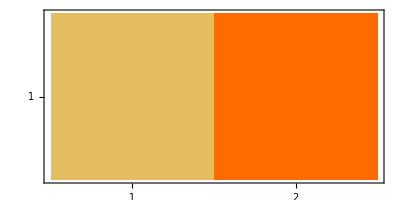

3

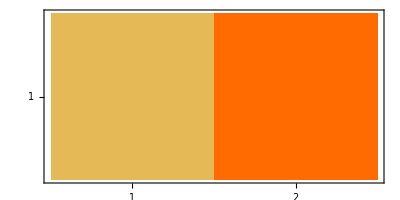

5

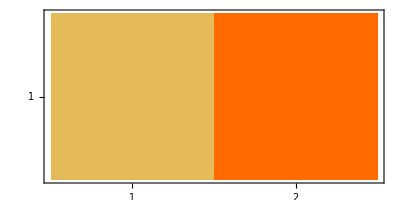

6

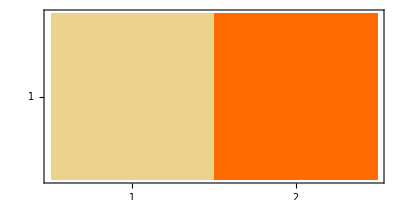

8

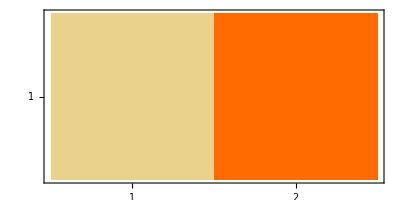

9

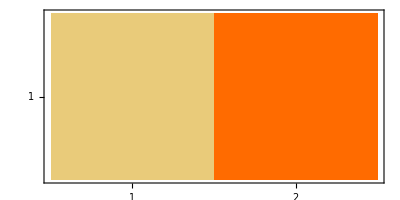

10

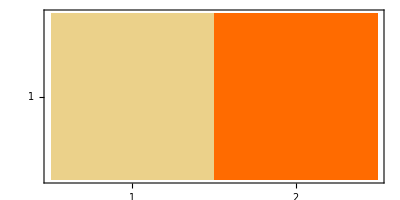

13

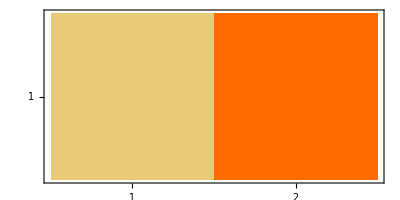

15

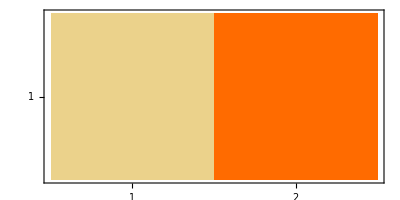

19

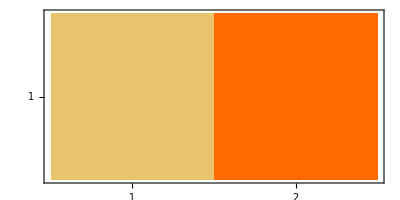

20

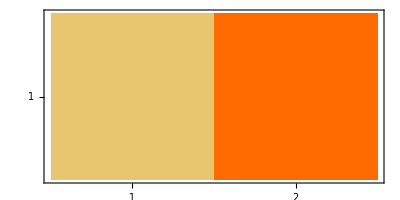

22

-Graphics-

25

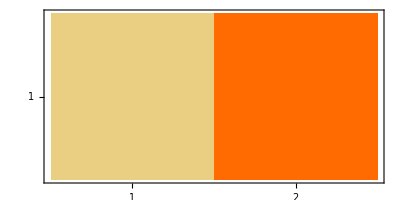

26

-Graphics-

29

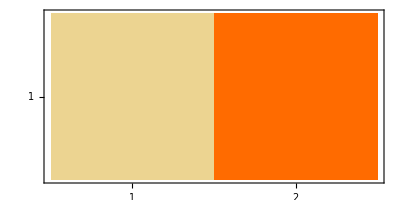

30

-Graphics-

32

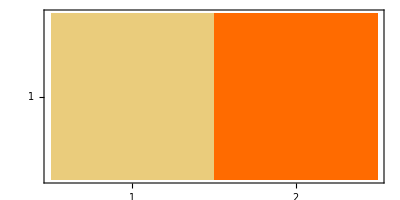

33

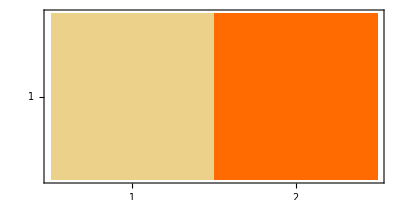

34

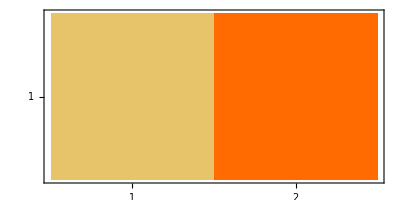

36

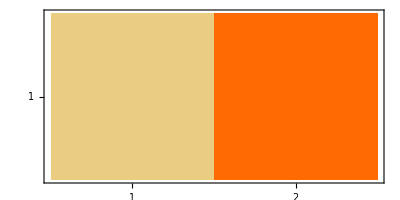

38

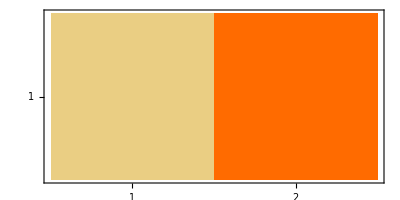

40

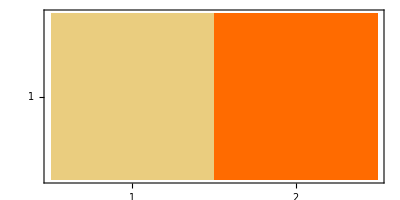

43

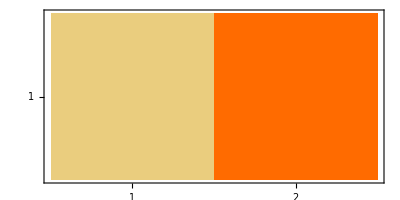

47

-Graphics-

48

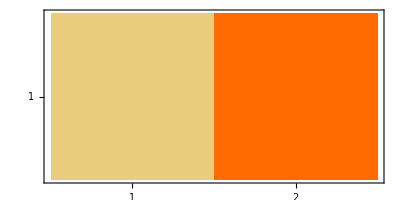

50

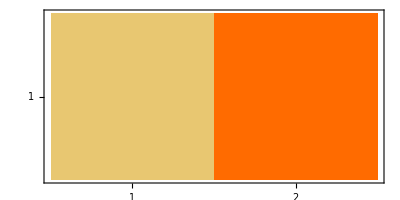

52

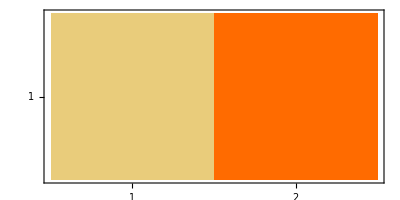

56

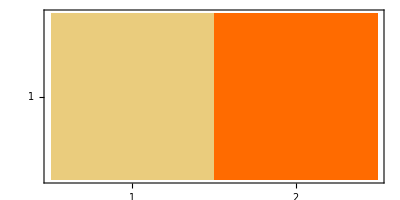

58

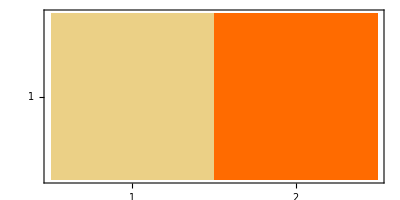

60

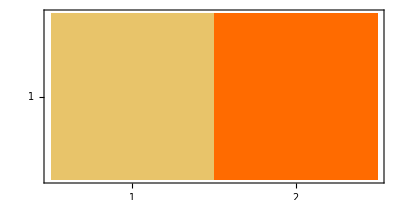

62

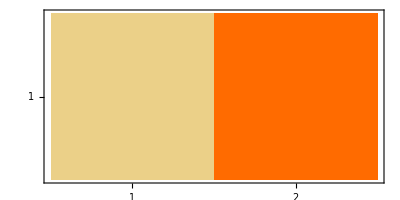

63

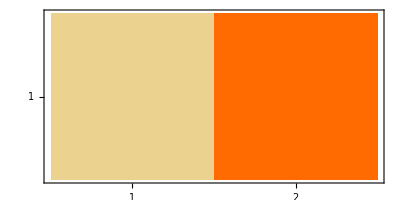

65

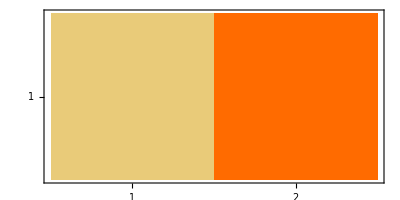

66

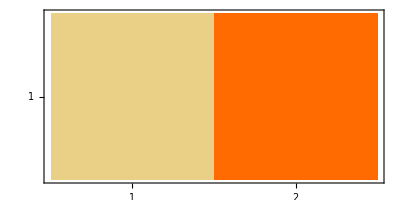

67

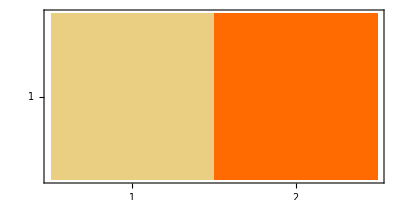

70

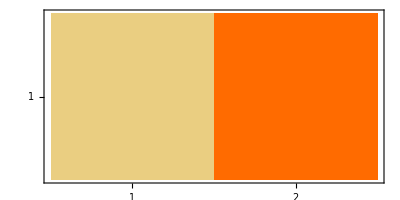

72

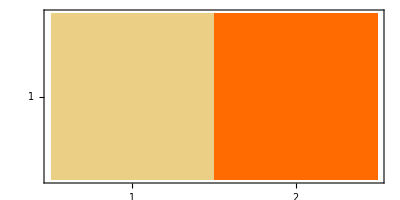

73

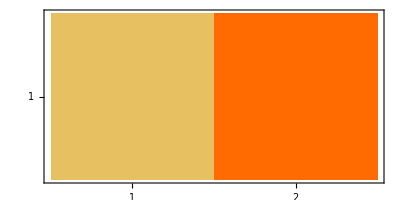

75

-Graphics-

78

-Graphics-

80

-Graphics-

84

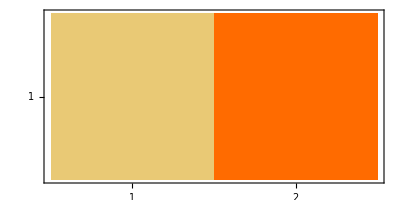

87

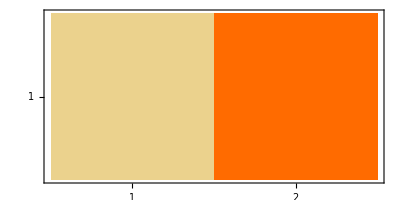

88

-Graphics-

91

-Graphics-

95

-Graphics-

96

-Graphics-

98

-Graphics-

```mathematica
For[Work= Wex;i=1, i<1000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];a4=RandomReal[{0.0001,0.4999}];t=RandomReal[{0,2π}];
Work= Wex; If[Work>0 ,{Popa1[i_]:=Popa1[i]=Abs[a1-a3]+Abs[a3-a2]+Abs[a3-a4];Table[Popa1[i],i];W4qb[i_] :=W4qb[i]= Work;Table[W4qb[i],i]},Null];Clear[Work,a1,a2,a3,a4,t]];
ListPlot[Table[{i,W4qb[i]},{i,1000}]]
ListPlot[Table[{Popa1[i],i},{i,1000}]]
```

```mathematica
0cde3\
```

```mathematica
ListPlot[%1173]
```

```mathematica
Print[MatrixPlot[RHOT]];Print[WEX1];Print[WEX2];
```

5

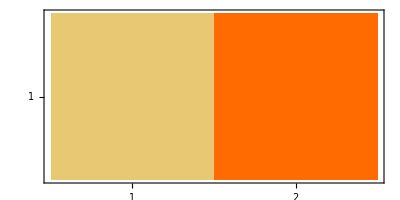

9

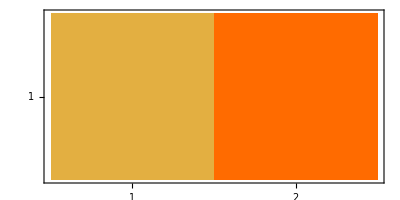

11

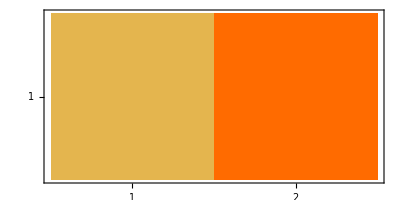

14

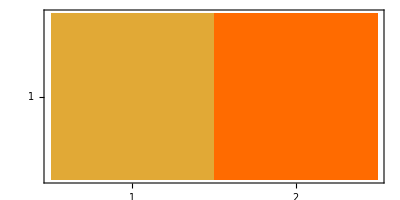

15

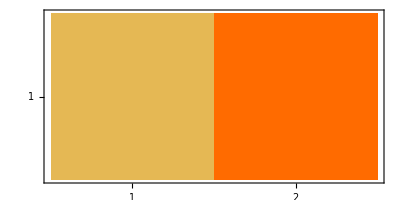

18

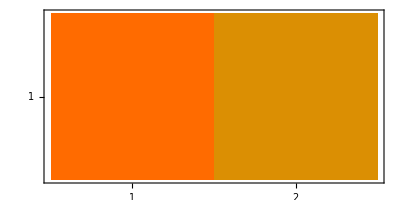

22

-Graphics-

23

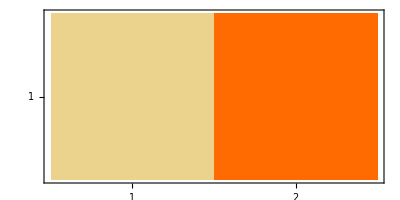

27

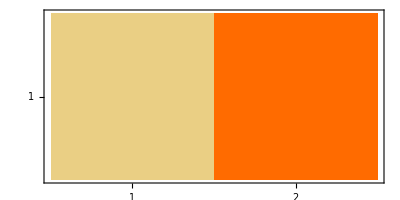

35

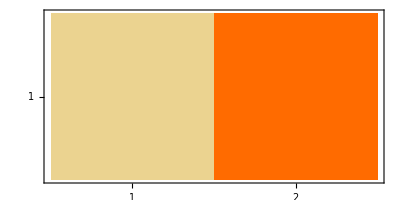

37

-Graphics-

41

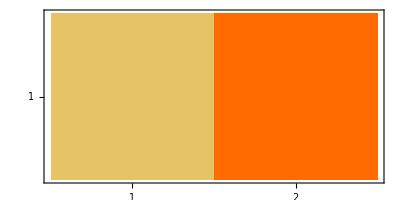

42

-Graphics-

60

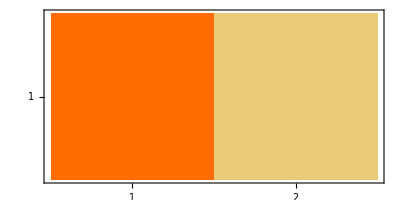

69

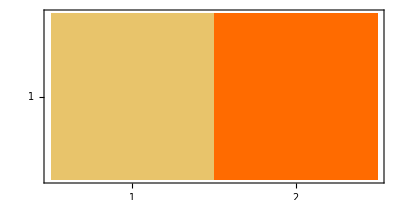

72

-Graphics-

74

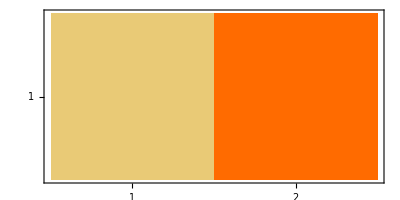

75

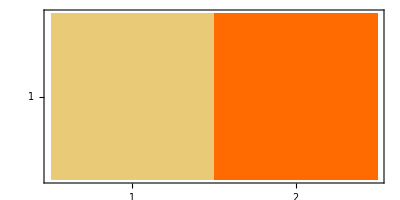

79

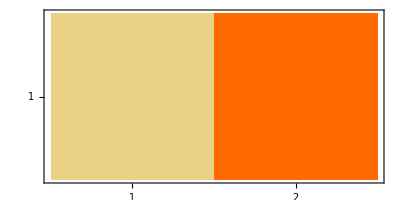

83

-Graphics-

87

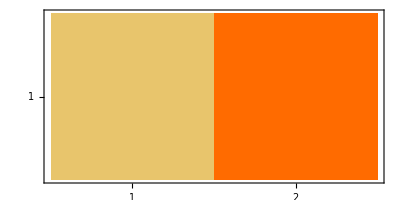

103

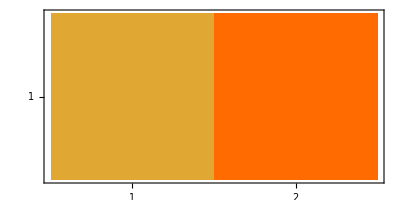

110

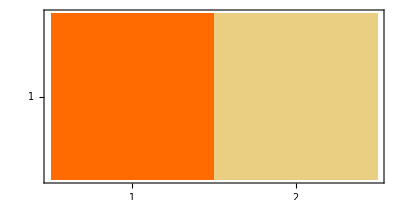

111

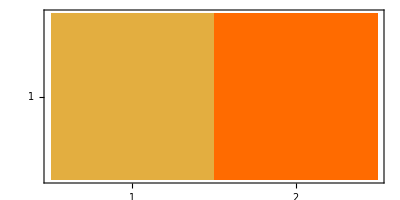

112

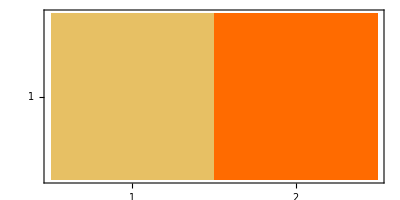

120

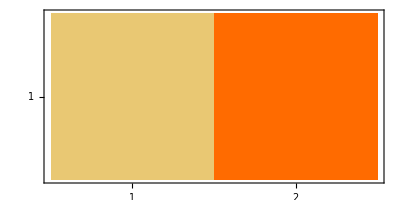

130

-Graphics-

144

-Graphics-

145

-Graphics-

157

-Graphics-

161

-Graphics-

164

-Graphics-

172

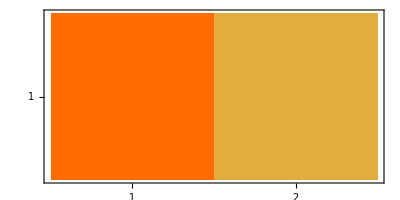

176

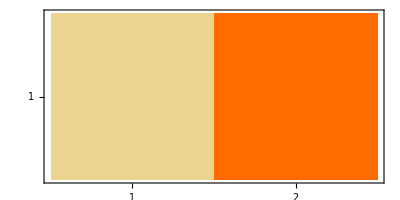

183

-Graphics-

188

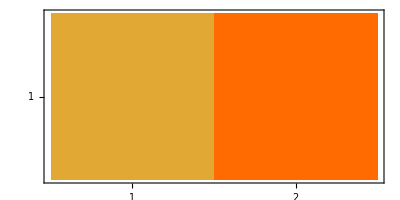

197

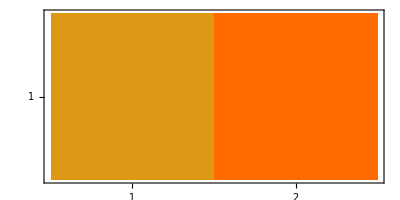

198

-Graphics-

202

-Graphics-

204

-Graphics-

206

-Graphics-

208

-Graphics-

212

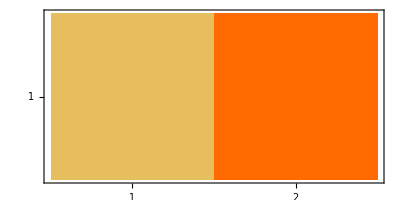

213

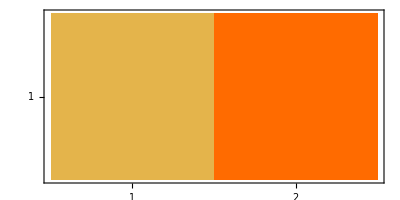

215

-Graphics-

218

-Graphics-

223

-Graphics-

224

-Graphics-

228

-Graphics-

229

-Graphics-

234

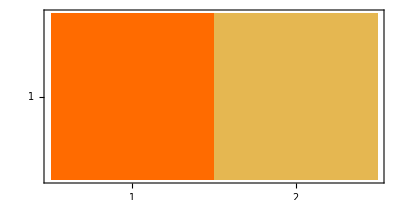

239

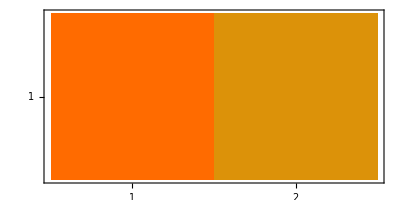

253

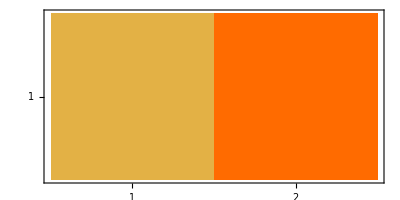

255

-Graphics-

259

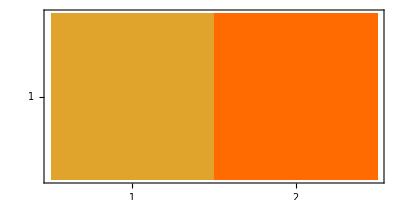

260

-Graphics-

261

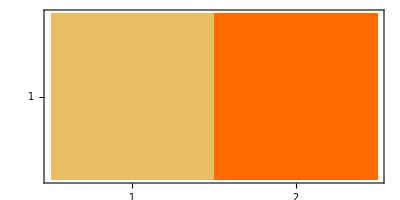

262

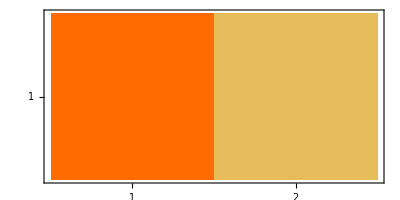

265

-Graphics-

268

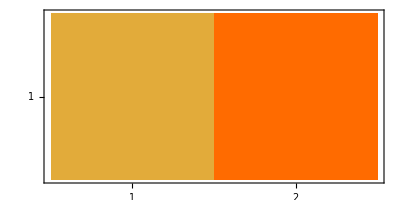

280

-Graphics-

288

-Graphics-

291

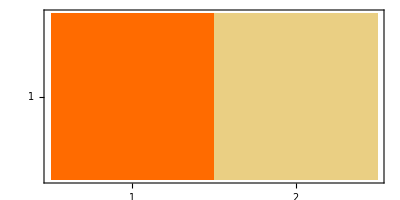

309

-Graphics-

312

-Graphics-

313

-Graphics-

316

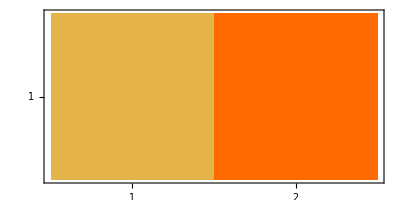

318

-Graphics-

326

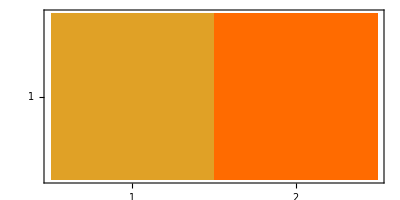

328

-Graphics-

348

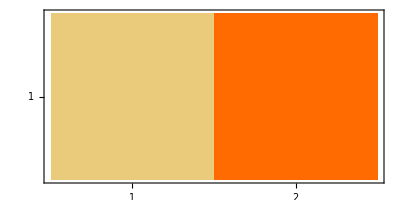

350

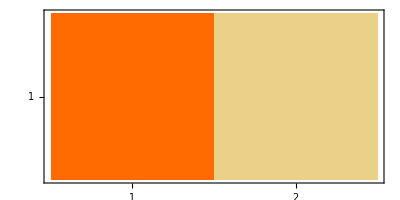

351

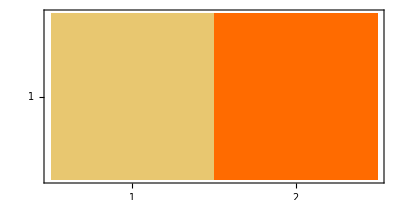

353

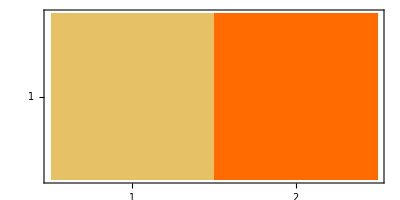

365

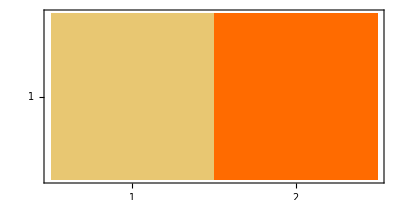

369

-Graphics-

383

-Graphics-

384

-Graphics-

390

-Graphics-

406

-Graphics-

410

-Graphics-

419

-Graphics-

423

-Graphics-

428

-Graphics-

434

-Graphics-

439

-Graphics-

443

-Graphics-

445

-Graphics-

449

-Graphics-

451

-Graphics-

457

-Graphics-

462

-Graphics-

468

-Graphics-

470

-Graphics-

480

-Graphics-

482

-Graphics-

485

-Graphics-

487

-Graphics-

489

-Graphics-

493

-Graphics-

496

-Graphics-

518

-Graphics-

522

-Graphics-

526

-Graphics-

527

-Graphics-

528

-Graphics-

529

-Graphics-

544

-Graphics-

550

-Graphics-

557

-Graphics-

563

-Graphics-

565

-Graphics-

566

-Graphics-

568

-Graphics-

570

-Graphics-

571

-Graphics-

580

-Graphics-

582

-Graphics-

594

-Graphics-

596

-Graphics-

604

-Graphics-

618

-Graphics-

621

-Graphics-

632

-Graphics-

633

-Graphics-

637

-Graphics-

643

-Graphics-

655

-Graphics-

658

-Graphics-

660

-Graphics-

662

-Graphics-

674

-Graphics-

681

-Graphics-

683

-Graphics-

685

-Graphics-

690

-Graphics-

704

-Graphics-

709

-Graphics-

714

-Graphics-

720

-Graphics-

722

-Graphics-

726

-Graphics-

731

-Graphics-

732

-Graphics-

733

-Graphics-

738

-Graphics-

739

-Graphics-

749

-Graphics-

753

-Graphics-

765

-Graphics-

775

-Graphics-

783

-Graphics-

785

-Graphics-

786

-Graphics-

788

-Graphics-

789

-Graphics-

790

-Graphics-

807

-Graphics-

809

-Graphics-

814

-Graphics-

817

-Graphics-

823

-Graphics-

826

-Graphics-

838

-Graphics-

847

-Graphics-

858

-Graphics-

865

-Graphics-

869

-Graphics-

879

-Graphics-

881

-Graphics-

882

-Graphics-

884

-Graphics-

887

-Graphics-

889

-Graphics-

899

-Graphics-

905

-Graphics-

918

-Graphics-

923

-Graphics-

933

-Graphics-

934

-Graphics-

935

-Graphics-

948

-Graphics-

953

-Graphics-

960

-Graphics-

962

-Graphics-

971

-Graphics-

978

-Graphics-

```mathematica
Clear[a1,a2,a3,a4,a5,a6,at,θ,i,RHOT,Qubit1,Qubit2,Qubit4,Qubit5,QubitT1,QubitT2,QubitGrad1,QubitGrad2]
Temp[h_]:= 1/(Log[(1-h)/h])
a1=RandomReal[{0.0001,0.4999}];
a2=RandomReal[{0.0001,0.4999}];
a3=RandomReal[{0.0001,0.4999}];
a4=RandomReal[{0.0001,0.4999}];
a5=RandomReal[{0.0001,0.4999}];
a6=RandomReal[{0.0001,0.4999}];
at=RandomReal[{0.0001,0.4999}];
For[RHOT=RHO;start=1,start<100,start++,Qubitsubsys1=TraceSystem[RHOT,{3,4,5,6,7,8}];QubitT1=TraceSystem[RHOT,{1,2,4,5,6,7,8}];Qubitsubsys2=TraceSystem[RHOT,{1,2,3,4,7,8}];QubitT2=TraceSystem[RHOT,{1,2,3,4,5,6,8}];
T1=QubitT1[[2,2]];
T2=QubitT2[[2,2]];
ExtWorkInSubSys1= Temp[T1]*Tr[Qubitsubsys1.MatrixLog[Qubitsubsys1]]- Temp[T1]* Tr[Qubitsubsys1.MatrixLog[KroneckerProduct[{{1-T1,0},{0,T1}},{{1-T1,0},{0,T1}}] ]   ]//FullSimplify; ExtWorkInSubSys2= Temp[T2]*Tr[Qubitsubsys2.MatrixLog[Qubitsubsys2]]- Temp[T1]* Tr[Qubitsubsys2.MatrixLog[KroneckerProduct[{{1-T2,0},{0,T2}},{{1-T2,0},{0,T2}}] ]   ]//FullSimplify;
WIN1=ExtWorkInSubSys1;
WIN2=ExtWorkInSubSys2;ChoiceOfUnitary=RandomChoice[{1,2}];θ=RandomReal[{0,2π}];If[ChoiceOfUnitary ==1,RHOT=SparseArray[TotalInteractionUnitaryForCase1].SparseArray[RHOT].Transpose[SparseArray[TotalInteractionUnitaryForCase1]],RHOT=SparseArray[TotalInteractionUnitaryForCase2].SparseArray[RHOT].Transpose[SparseArray[TotalInteractionUnitaryForCase2]]
];Qubitsubsys1=TraceSystem[RHOT,{3,4,5,6,7,8}];QubitT1=TraceSystem[RHOT,{1,2,4,5,6,7,8}];Qubitsubsys2=TraceSystem[RHOT,{1,2,3,4,7,8}];QubitT2=TraceSystem[RHOT,{1,2,3,4,5,6,8}];
T1=QubitT1[[2,2]];
T2=QubitT2[[2,2]];
ExtWorkInSubSys1= Temp[T1]*Tr[Qubitsubsys1.MatrixLog[Qubitsubsys1]]- Temp[T1]* Tr[Qubitsubsys1.MatrixLog[KroneckerProduct[{{1-T1,0},{0,T1}},{{1-T1,0},{0,T1}}] ]   ]//FullSimplify; ExtWorkInSubSys2= Temp[T2]*Tr[Qubitsubsys2.MatrixLog[Qubitsubsys2]]- Temp[T1]* Tr[Qubitsubsys2.MatrixLog[KroneckerProduct[{{1-T2,0},{0,T2}},{{1-T2,0},{0,T2}}] ]   ]//FullSimplify;
WFIN1=ExtWorkInSubSys1;
WFIN2=ExtWorkInSubSys2;
WEX1=WFIN1-WIN1;
WEX2=WFIN2-WIN2;
Qubit1=TraceSystem[RHOT,{2,3,4,5,6,7,8}];
Qubit4= TraceSystem[RHOT,{1,2,3,4,6,7,8}];
Qubit2=TraceSystem[RHOT,{1,3,4,5,6,7,8}];
QubitGrad1=TraceSystem[RHOT,{1,2,3,5,6,7,8}];
Qubit5=TraceSystem[RHOT,{1,2,3,4,5,7,8}];
QubitGrad2=TraceSystem[RHOT,{1,2,3,4,5,6,7}];DensityMatrixFull = {{Qubit1[[2,2]],QubitT1[[2,2]],Qubit4[[2,2]],QubitT2[[2,2]]},{Qubit2[[2,2]],QubitGrad1[[2,2]],Qubit5[[2,2]],QubitGrad2[[2,2]]}};WorkMatrix = {{WEX1,WEX2}};If[WEX1>0&&WEX2>0,
Print[start];Print[MatrixPlot[WorkMatrix]],Null] ]
```

```mathematica
LinguisticAssistant
```

```mathematica
ChoiceOfUnitary=RandomChoice[{1,2}]
```

2